# Trend duration analysis

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

ADPiValues[data_,window_,skip_ :1]:= Module[{part, cutdates,ad},
part = Partition[data,window,skip];
ad = ParallelMap[Quiet[AndersonDarlingTest[#-1,GeometricDistribution[0.5]]] &,part];
Return[ad];
];

DatedADPiValues[data_,window_,skip_ :1]:= Module[{part, cutdates,ad,dates},
part = Partition[data,window,skip];
ad = ParallelMap[Quiet[AndersonDarlingTest[#-1,GeometricDistribution[0.5]]] &,part[[All,All,2]]];
dates = Map[Last,part[[All,All,1]]];

Return[Transpose[{dates,ad}]];
];
SignRatio[returns_]:= N[Count[Map[Sign,returns],1]/Length[returns]];
PriceChangeRatio[returns_]:=Total[Select[returns,Positive]]/Total[Abs[returns]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

DatedTrendDuration[datedprices]
DatedTrendDuration[dates, prices]
calculates TrendDuration with date info.

## Database

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_NASDAQ_MXX_NIKKEI_dataset.wdx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","NASDAQ Composite","IPC","Nikkei 225"};
```

Date fixer: There are no dates in the original dataset, this generates the intermediate dates.

```mathematica
GenerateDaysBetween[firstDate_DateObject,lastDate_DateObject,length_]:=Block[{dayRange,dayCount,ratio},
dayRange = DayRange[firstDate,lastDate];
dayCount = DayCount[firstDate,lastDate];
ratio = dayCount/length;
Table[Part[dayRange,Floor[i*ratio]],{i,length}]
];
AddToDataset[database,"Dates",GenerateDaysBetween[DateObject[#1],DateObject[#2],Length[#3]]&,{"FirstDate","LastDate","Prices"}];
```

Important dates

```mathematica
rules = {"Black Monday"->"(a)","Japanese asset\nprice bubble"-> "(b)","Tequila effect"->"(c)","Dotcom bubble"->"(d)","Subprime crisis"->"(e)","Brexit"->"(f)"};
dateNames = {"Black Monday","Japanese asset\nprice bubble","Tequila effect","Dotcom bubble","Subprime crisis","Brexit"}/.rules;
dateObjects = {DateObject[{1987,10,19},"Day","Gregorian",-6.],DateObject[{1990,1,1},"Day","Gregorian",-5.],DateObject[{1994,1,1},"Day","Gregorian",-5.],DateObject[{2000,3,10},"Day","Gregorian",-5.],DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2016,6,23},"Day","Gregorian",-5.]};

AddKeyToMarket[database[[1]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[1]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[2]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[2]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[3]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[3]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[4]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[4]],"ImportantDates"->dateObjects];
```

## p-values

Figure 4.

```mathematica
CalculateADPiValues[dates_,prices_,window_]:=Module[{trendDuration,p,adValues},
trendDuration = DatedTrendDuration[dates,prices];
adValues = DatedADPiValues[trendDuration,window,1];
Return[adValues];
];

CalculateADPiValuesAndFilter[dates_,prices_,window_]:=Module[{trendDuration,p,adValues},
(* Nota: No se encontró ninguna diference al usar este filtrado *)
trendDuration = DatedTrendDuration[dates,prices];
trendDuration = DeleteCases[trendDuration,{_,x_}/;x>14];
adValues = DatedADPiValues[trendDuration,window,1];
Return[adValues];
];
```

```mathematica
ClosestDate[list_,date_]:=First[MinimalBy[list,Abs[QuantityMagnitude[DateDifference[First[#],date]]]&]];
FixZeros[{n_,m_}]:=If[m==0,{n,2.381429155762227*^-6},{n,m}];

PlotADValues[market_]:=Block[{legend,crashLabels,uppList,plotData,firstDate,lastDate},
If[market["Name"] == "DJIA",
legend = Placed[LineLegend[{None,"α = 0.1","α = 0.05","α = 0.01"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}];
,
legend = None
];

{firstDate,lastDate} = {First[First[market["ADValues"]]],First[Last[market["ADValues"]]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];

crashLabels = MapThread[
Callout[
FixZeros@ClosestDate[market["ADValues"],#1],#2,Above,
LeaderSize->35,CalloutStyle->Directive[Black,Thick],Appearance->"SlantedLabel"
]&,
{market["ImportantDates"][[All,1]],market["ImportantDatesNames"]}
];

plotData = Join[{market["ADValues"]},uppList];

DateListLogPlot[
plotData,
PlotRange->{Automatic,{Automatic,1}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["π-Value",15]},
BaseStyle->FontSize->13,
PlotLabel->market["Name"],
ImageSize->500,
Joined->{True,True,True,True,False},
PlotStyle->colors,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->legend,
FrameTicks->True
]
];
```

```mathematica
AddToDataset[database,"ADValues",CalculateADPiValues[#1,#2,252]&,{"Dates","Prices"}];
```

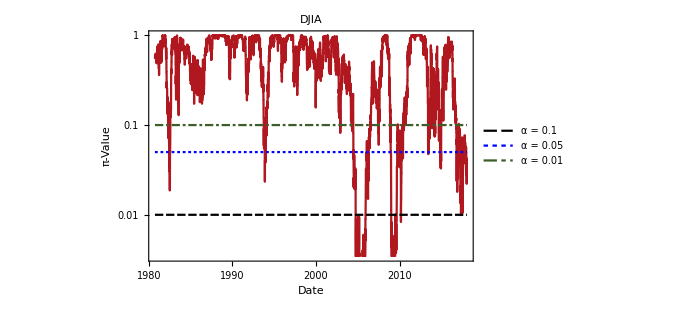
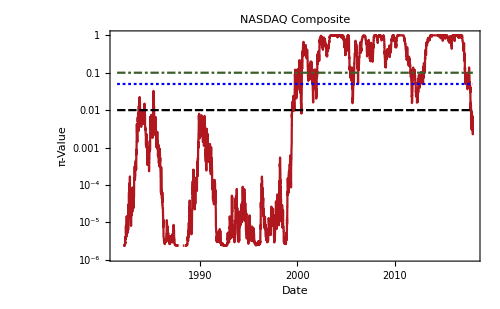
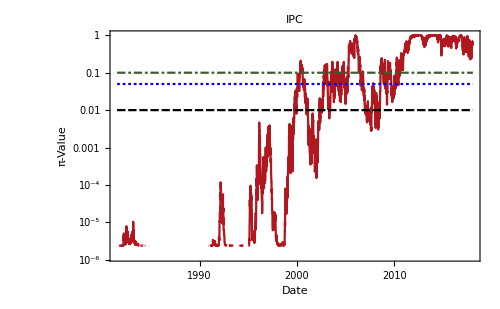
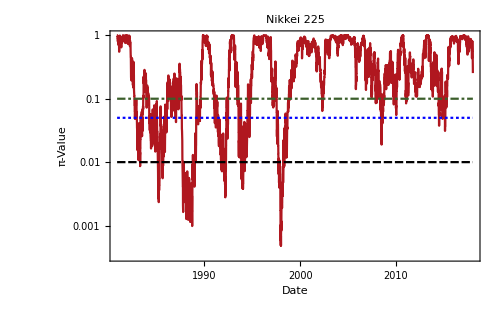

```mathematica
Map[PlotADValues,database]
```

## Distribution

Figure 3.

```mathematica
UpwardTrendDuration[prices_] := Module[{splitted,posTrends},
splitted =Split[Sign[SimpleReturns[prices]]];
posTrends = Select[splitted,Apply[Or,Positive[#]]&];
Return[Map[Length,posTrends]];
];
DownwardTrendDuration[prices_] := Module[{splitted,negTrends},
splitted =Split[Sign[SimpleReturns[prices]]];
negTrends = Select[splitted,Apply[Or,Negative[#]]&];
Return[Map[Length,negTrends]];
];
TrendHistogramPoints[prices_,durationFunction_]:=Module[{trendDuration,histogramList},
trendDuration = durationFunction[prices] - 1;
histogramList = Map[{#,Count[trendDuration,#]/Length[trendDuration]}&,DeleteDuplicates[trendDuration]];
Return[histogramList];
];

EstimateP[trendDuration_]:=Module[{p},p/.FindDistributionParameters[trendDuration,GeometricDistribution[p]]];
EstimateP[prices_,durationFunction_]:=EstimateP[durationFunction[prices] - 1];
GoodnessOfFit[prices_,durationFunction_]:=DistributionFitTest[durationFunction[prices]-1,GeometricDistribution[EstimateP[prices,durationFunction]]];

FitTrend[prices_,durationFunction_]:=Module[{trendDuration,p,fittedPts},
trendDuration = durationFunction[prices] - 1;
p = EstimateP[trendDuration];
fittedPts = Table[{k,PDF[GeometricDistribution[p],k]},{k,0,Max[trendDuration]}];
Return[fittedPts];
];

PlotTrendDistribution[trendDatabase_,direction_,color_:Red]:=Block[{fit,histogram,estimatedP,legend},
fit = If[direction=="Upward","UpwardFit","DownwardFit"];
histogram = If[direction=="Upward","UpwardHistogram","DownwardHistogram"];
estimatedP = If[direction=="Upward","UpwardEstimatedP","DownwardEstimatedP"];

If[trendDatabase["Name"] == "DJIA",
legend = Placed[
LineLegend[{"Fit","Histogram"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],
{Left,Bottom}
];
,
legend = None
];

ListLogPlot[
{trendDatabase[fit],trendDatabase[histogram]},
Joined->{True,False},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Duration (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->trendDatabase["Name"],
PlotStyle->{color,{PointSize[Large],Black}},
Epilog->{Inset[Framed[Text[Style["p̂ = "<>ToString[trendDatabase[estimatedP]],14]],RoundingRadius->1,Background->RGBColor[1,1,1,.8]],Scaled[{0.8,.8}]]},
ImageSize->500,
PlotLegends->legend,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
];
```

Upward trends

```mathematica
AddToDataset[database,"UpwardHistogram",TrendHistogramPoints[#,UpwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"UpwardFit",FitTrend[#,UpwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"UpwardEstimatedP",EstimateP[#,UpwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"UpwardGoodnessFit",GoodnessOfFit[#,UpwardTrendDuration]&,{"Prices"}];
```

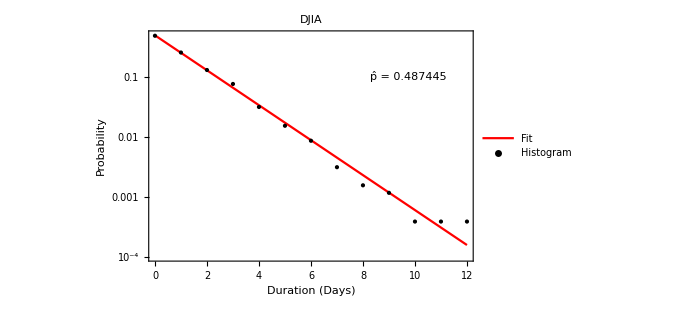
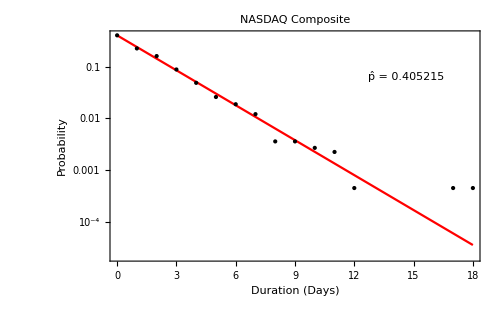
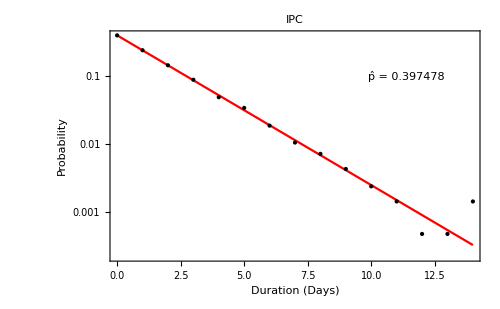
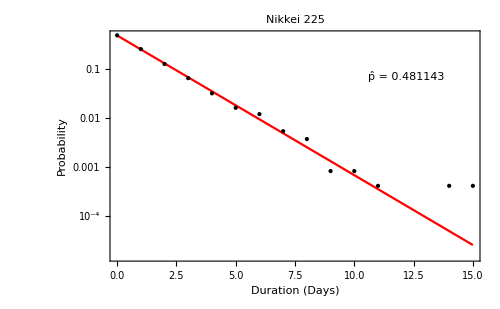

```mathematica
Map[PlotTrendDistribution[#,"Upward",Red]&,database]
```

```mathematica
Dataset@database[[All,{"Name","UpwardGoodnessFit"}]]
```

Dataset[<>]

Downward trends

```mathematica
AddToDataset[database,"DownwardHistogram",TrendHistogramPoints[#,DownwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"DownwardFit",FitTrend[#,DownwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"DownwardEstimatedP",EstimateP[#,DownwardTrendDuration]&,{"Prices"}];
AddToDataset[database,"DownwardGoodnessFit",GoodnessOfFit[#,DownwardTrendDuration]&,{"Prices"}];
```

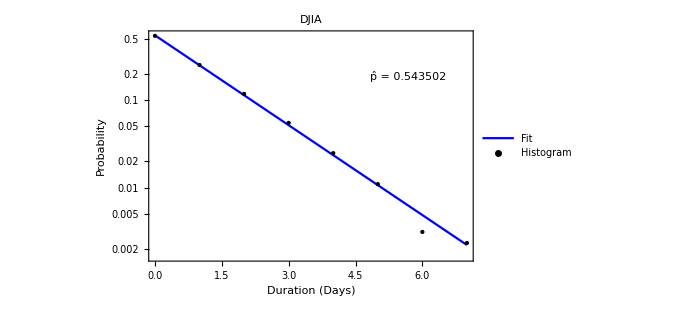
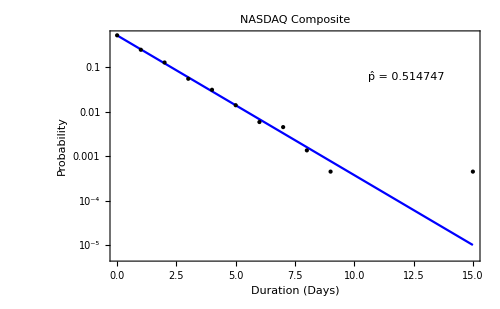
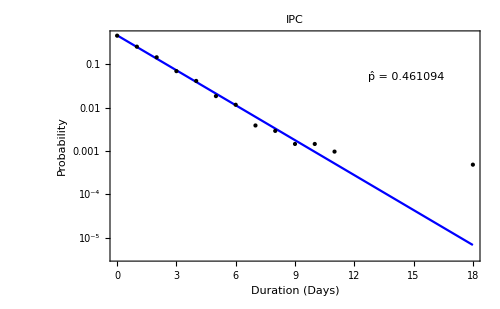
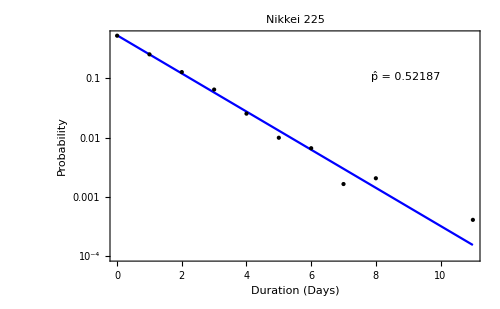

```mathematica
Map[PlotTrendDistribution[#,"Downward",Blue]&,database]
```

```mathematica
Dataset@database[[All,{"Name","DownwardGoodnessFit"}]]
```

Dataset[<>]

```mathematica
nasdaq = database[[3]]["Prices"];
```

```mathematica
Sort@DeleteDuplicates@UpwardTrendDuration[nasdaq]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
Sort@DeleteDuplicates@DownwardTrendDuration[nasdaq]
```

{1,2,3,4,5,6,7,8,9,10,11,12,19}

## Trend sign

Figure. 2.

```mathematica
SignChangeInTime[prices_,window_,skip_:1]:=Module[{returns,part,ratios},
returns = Returns[prices];
part = Partition[returns,window,skip];
ratios = Map[SignRatio,part];
Return[ratios];
];
```

```mathematica
AddToDataset[database,"PriceChangeRatio",SignChangeInTime[#,252,5]&,{"Prices"}];
```

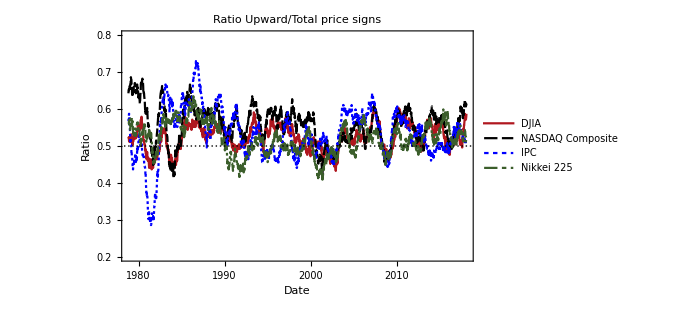

```mathematica
DateListPlot[
database[[All,"PriceChangeRatio"]],
{First[database]["FirstDate"],First[database]["LastDate"]},
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotLabel->"Ratio Upward/Total price signs",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.2,0.8}}
]
```

## Trend example

Figure. 1

```mathematica
smallSample = Take[database[[2]]["Prices"],50];
smallSampleInTime = Transpose[{Range[50],smallSample}];
smallTr = DatedTrendReturns[Range[50],smallSample];
pricesInTr = smallSampleInTime[[smallTr[[All,1]]]];
```

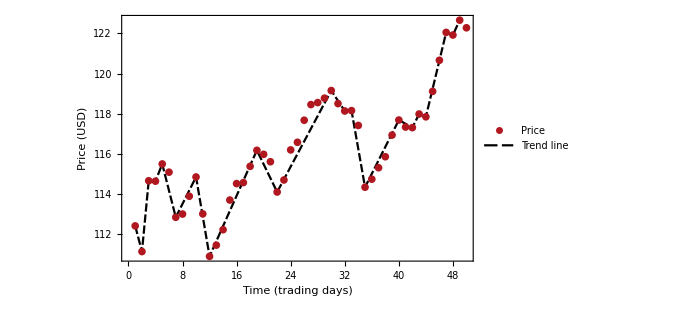

```mathematica
figure = ListPlot[
{smallSampleInTime,pricesInTr},
Joined->{False, True},
ImageSize->500,
PlotTheme->"Monochrome",
FrameLabel->{Style["Time (trading days)",15],Style["Price (USD)",15]},
Frame->True,BaseStyle->FontSize->14,
TicksStyle->Large,
PlotMarkers->None, 
PlotStyle->colors,
PlotLegends->Placed[LineLegend[{"Price", "Trend line"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}]
]
```

## Samples size

```mathematica
GetInfo[market_]:=Module[{name,sampleSize,partitionSize,firstDate, lastDate},
name = market["Name"];
sampleSize = Length[market["Prices"]];
partitionSize = Length[Partition[TrendDuration[market["Prices"]],500,1]];
firstDate = DateString[market["FirstDate"],"ISODate"];
lastDate = DateString[market["LastDate"],"ISODate"];

Return[{name,sampleSize,partitionSize, firstDate,lastDate}];
];
```

```mathematica
info = Map[GetInfo,database];
Grid[Join[{{"Market name","Sample size","Partition size","First date","Last date"}},info],Background->{None,{Gray}}]
```

Market name | Sample size | Partition size | First date | Last date
DJIA | 9932 | 4630 | 1978-10-30 | 2018-01-23
NASDAQ Composite | 9895 | 4003 | 1978-10-30 | 2018-01-23
IPC | 9795 | 3716 | 1978-10-30 | 2018-01-23
Nikkei 225 | 9682 | 4349 | 1978-10-30 | 2018-01-23

## Check parameter estimation

```mathematica
UpwardDatedTrendDuration[dates_,prices_] := Module[{simpleReturns,splitted,posTrends,result},
simpleReturns = DatedSimpleReturns[dates,prices];
splitted =SplitBy[MapAt[Sign,simpleReturns,{All,2}],Last];
posTrends = Select[splitted,Apply[Or,Positive[#[[All,2]]]]&];
result = Map[{#[[1,1]],Length[#]}&,posTrends];
Return[result];
];
DownwardDatedTrendDuration[dates_,prices_] := Module[{simpleReturns,splitted,negTrends,result},
simpleReturns = DatedSimpleReturns[dates,prices];
splitted =SplitBy[MapAt[Sign,simpleReturns,{All,2}],Last];
negTrends = Select[splitted,Apply[Or,Negative[#[[All,2]]]]&];
result = Map[{#[[1,1]],Length[#]}&,negTrends];
Return[result];
];

EstimatePInTime[dates_,prices_,trendDurationFunction_,window_,skip_]:=Module[{p,ps,trendDuration,part,datesPart,pricesPart,outDates},
trendDuration = trendDurationFunction[dates,prices];
part = Partition[trendDuration,window,skip];
datesPart = part[[All,All,1]];
pricesPart = part[[All,All,2]];

outDates = Map[Last,part[[All,All,1]]];
ps = Map[p/.FindDistributionParameters[#-1,GeometricDistribution[p]]&,pricesPart];

Return[Transpose[{outDates,ps}]];
];
EstimateGoodnessOfFitInTime[dates_,prices_,trendDurationFunction_,window_,skip_]:=Module[{fit,p,ps,trendDuration,part,datesPart,pricesPart,outDates},
trendDuration = trendDurationFunction[dates,prices];
part = Partition[trendDuration,window,skip];
datesPart = part[[All,All,1]];
pricesPart = part[[All,All,2]];

outDates = Map[Last,part[[All,All,1]]];
ps = Map[
(
fit = p/.FindDistributionParameters[#-1,GeometricDistribution[p]];
DistributionFitTest[#-1,GeometricDistribution[fit]]
)&,
pricesPart
];

Return[Transpose[{outDates,ps}]];
];
```

All

```mathematica
AddToDataset[database,"EstimatedPInTime",EstimatePInTime[#1,#2,DatedTrendDuration,252,10]&,{"Dates","Prices"}];
AddToDataset[database,"EstimateGoodnessOfFitInTime",EstimateGoodnessOfFitInTime[#1,#2,DatedTrendDuration,252,10]&,{"Dates","Prices"}];
```

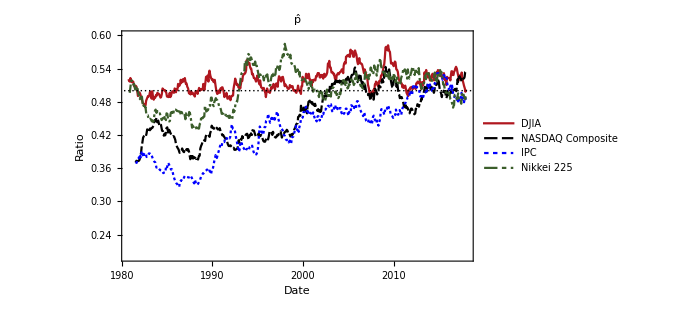

```mathematica
DateListPlot[
database[[All,"EstimatedPInTime"]],
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotLabel->"p̂",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.2,0.6}}
]
```

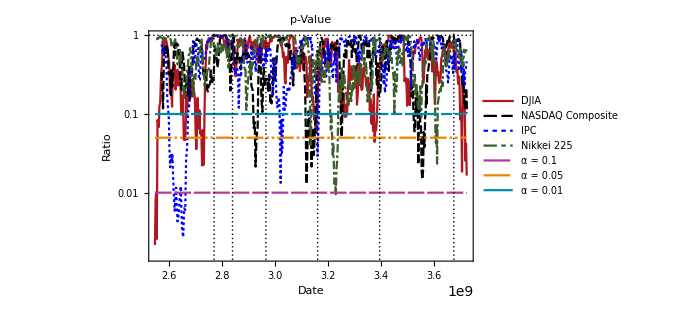

```mathematica
market = First[database];
{firstDate,lastDate} = {First[First[market["EstimateGoodnessOfFitInTime"]]],First[Last[market["EstimateGoodnessOfFitInTime"]]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];
plotData = Join[database[[All,"EstimateGoodnessOfFitInTime"]],uppList];

DateListLogPlot[
plotData,
PlotLegends->LineLegend[Join[database[[All,"Name"]],{"α = 0.1","α = 0.05","α = 0.01"}],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->"p-Value",
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.7000000000000001, 0.23, 0.59],RGBColor[0.92, 0.52, 0.],RGBColor[0., 0.55, 0.66]},
PlotMarkers->None,
Joined->True,
PlotRange->All,
GridLines->{dateObjects,{1}}
]
```

Both

```mathematica
AddToDataset[database,"EstimatedPositivePInTime",EstimatePInTime[#1,#2,UpwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
AddToDataset[database,"EstimatedNegativePInTime",EstimatePInTime[#1,#2,DownwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
```

```mathematica
PlotEstimatedP[market_]:=DateListPlot[
{market["EstimatedPositivePInTime"],market["EstimatedNegativePInTime"]},
PlotLegends->If[market["Name"] =="DJIA",
Placed[LineLegend[{"Upward","Downward"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
None
],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{dateObjects,{0.5}},
GridLinesStyle->{Directive[Dashed],Directive[Thick]},
PlotLabel->market["Name"],
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0, 0, 1]},
PlotMarkers->None,
Joined->True,
PlotRange->All
];
```

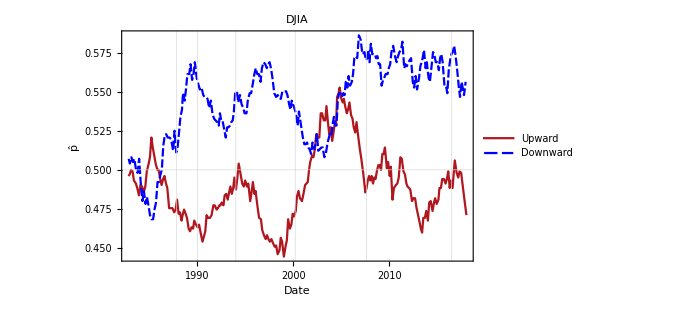
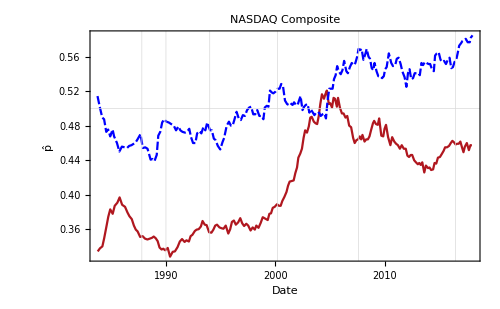
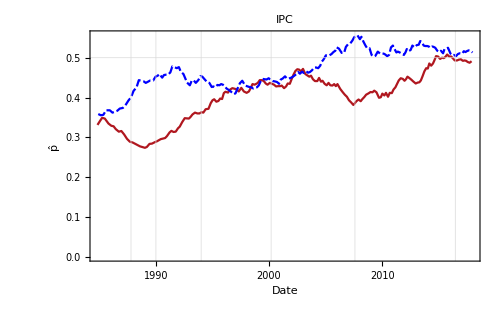
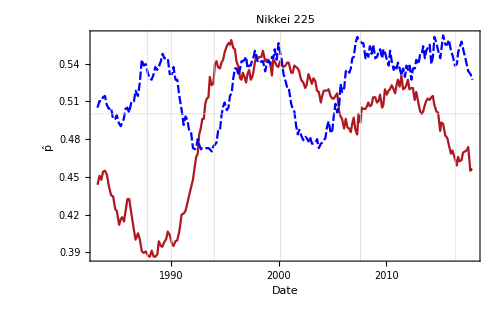

```mathematica
Map[PlotEstimatedP,database]
```

Positive

```mathematica
AddToDataset[database,"EstimatedUpwardPInTime",EstimatePInTime[#1,#2,UpwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
AddToDataset[database,"EstimateUpwardGoodnessOfFitInTime",EstimateGoodnessOfFitInTime[#1,#2,UpwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
```

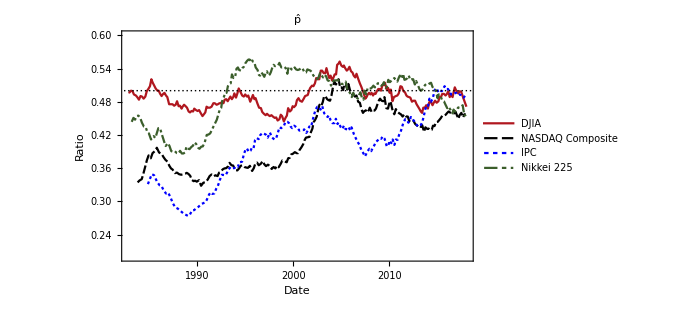

```mathematica
DateListPlot[
database[[All,"EstimatedUpwardPInTime"]],
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotLabel->"p̂",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.2,0.6}}
]
```

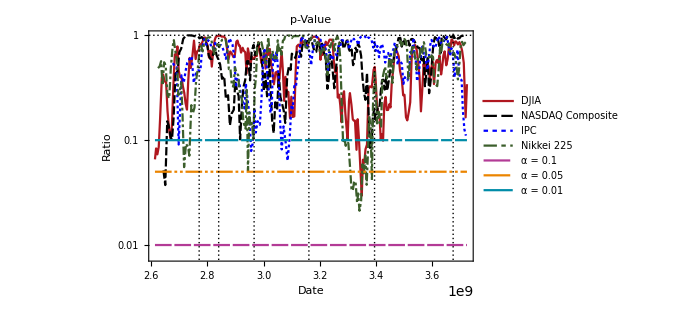

```mathematica
market = First[database];
{firstDate,lastDate} = {First[First[market["EstimateUpwardGoodnessOfFitInTime"]]],First[Last[market["EstimateUpwardGoodnessOfFitInTime"]]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];
plotData = Join[database[[All,"EstimateUpwardGoodnessOfFitInTime"]],uppList];

DateListLogPlot[
plotData,
PlotLegends->LineLegend[Join[database[[All,"Name"]],{"α = 0.1","α = 0.05","α = 0.01"}],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->"p-Value",
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.7000000000000001, 0.23, 0.59],RGBColor[0.92, 0.52, 0.],RGBColor[0., 0.55, 0.66]},
PlotMarkers->None,
Joined->True,
PlotRange->All,
GridLines->{dateObjects,{1}}
]
```

Negative

```mathematica
AddToDataset[database,"EstimatedDownwardPInTime",EstimatePInTime[#1,#2,DownwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
AddToDataset[database,"EstimateDownwardGoodnessOfFitInTime",EstimateGoodnessOfFitInTime[#1,#2,DownwardDatedTrendDuration,252,10]&,{"Dates","Prices"}];
```

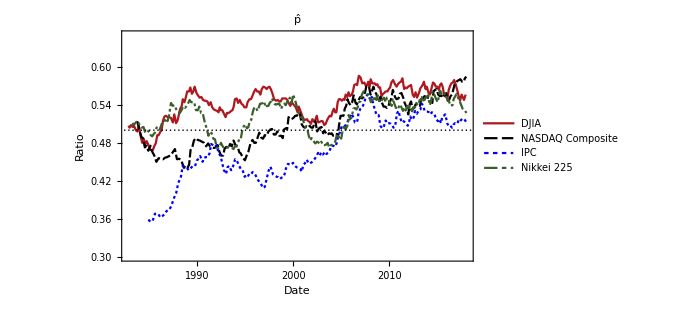

```mathematica
DateListPlot[
database[[All,"EstimatedDownwardPInTime"]],
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotLabel->"p̂",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.3,0.65}}
]
```

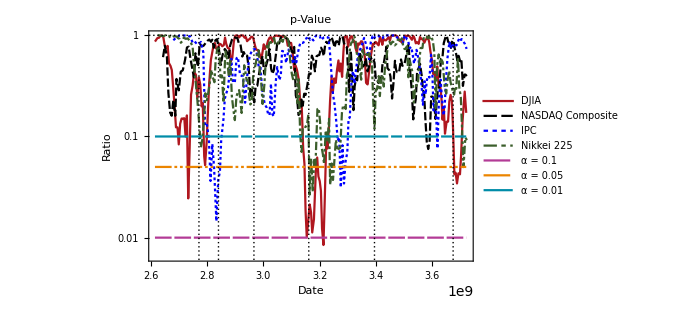

```mathematica
market = First[database];
{firstDate,lastDate} = {First[First[market["EstimateDownwardGoodnessOfFitInTime"]]],First[Last[market["EstimateDownwardGoodnessOfFitInTime"]]]};
uppList = Map[{{firstDate, #},{lastDate,#}}&,{0.01,0.05,0.1}];
plotData = Join[database[[All,"EstimateDownwardGoodnessOfFitInTime"]],uppList];

DateListLogPlot[
plotData,
PlotLegends->LineLegend[Join[database[[All,"Name"]],{"α = 0.1","α = 0.05","α = 0.01"}],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotLabel->"p-Value",
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.7000000000000001, 0.23, 0.59],RGBColor[0.92, 0.52, 0.],RGBColor[0., 0.55, 0.66]},
PlotMarkers->None,
Joined->True,
PlotRange->All,
GridLines->{dateObjects,{1}}
]
```

# Waiting time analysis

Distribution

Smooth histogram

```mathematica
DayLegends[n_Integer]:=Map[
If[# == 1,
StringJoin[ToString[#]," day"],
StringJoin[ToString[#]," days"]
]
&,
Range[n]
];
DayLegends[l_List]:=Map[
If[# == 1,
StringJoin[ToString[#]," day"],
StringJoin[ToString[#]," days"]
]
&,
l
];

WaitTime[prices_,duration_]:=Block[{td,grouped,dayIntervals},
td = TrendDuration[prices];
grouped = Drop[Split[td,#≠duration&],1];
dayIntervals = Map[Length,grouped]-1;
Return[dayIntervals];
];
WaitTimeForRuns[prices_,range_:4]:=Map[WaitTime[prices,#]&,Range[range]];

WaitTimeForMarket[market_]:=Block[{dist},
dist =WaitTimeForRuns[market["Prices"]];
SmoothHistogram[dist,1,
PlotRange->{{0,50},All},
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait",bigFontSize],Style["PDF",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[4],{Right,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
PlotLabel->market["Name"]
]
];
```

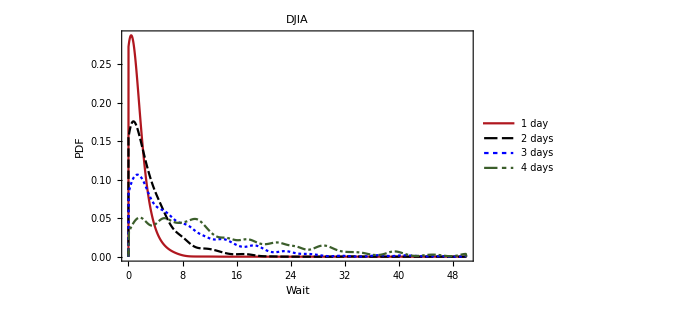
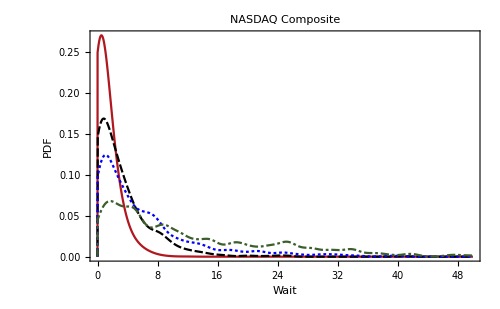
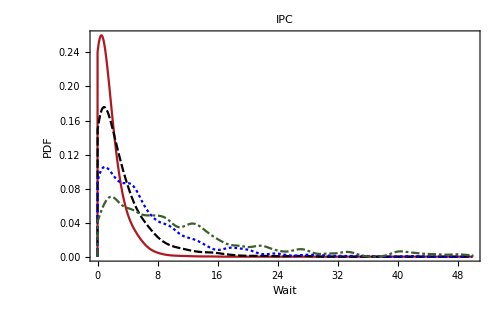
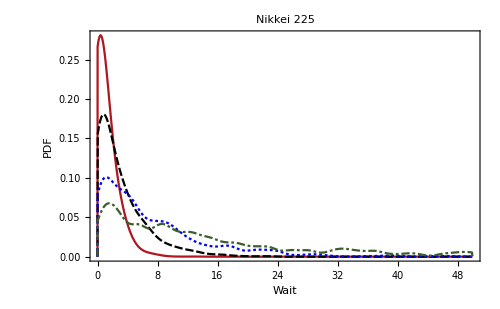

```mathematica
Map[WaitTimeForMarket,database]
```

Discrete

```mathematica
HistogramPoints[data_]:=SortBy[Map[{#,N@(Count[data,#]/Length[data])}&,DeleteDuplicates[data]],First];
GenerateFitted[p_,max_]:=Table[{k,PDF[GeometricDistribution[p],k]},{k,0,max}];
DiscreteHistogramWaitTime[market_]:=Block[{waitTimes,histogramPts,ps,legend,fitted},
waitTimes = WaitTimeForRuns[market["Prices"]];
histogramPts = Map[HistogramPoints,waitTimes];
ps = Map[EstimateP,waitTimes];
legend = MapThread[StringJoin[#1,", p̂ = ",ToString[#2]]&,{DayLegends[4],ps}];
fitted = Map[GenerateFitted[#,70]&,ps];

ListLogPlot[
Join[fitted,histogramPts],
Joined->{True,True,True,True,False,False,False,False},
PlotRange->{{0,70},{10^-5,1}},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait time (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->market["Name"],
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
ImageSize->600,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[LineLegend[legend,LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}]
]
];
```

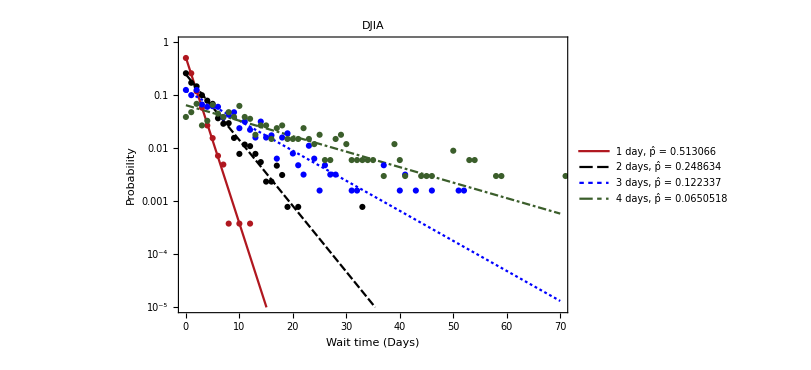
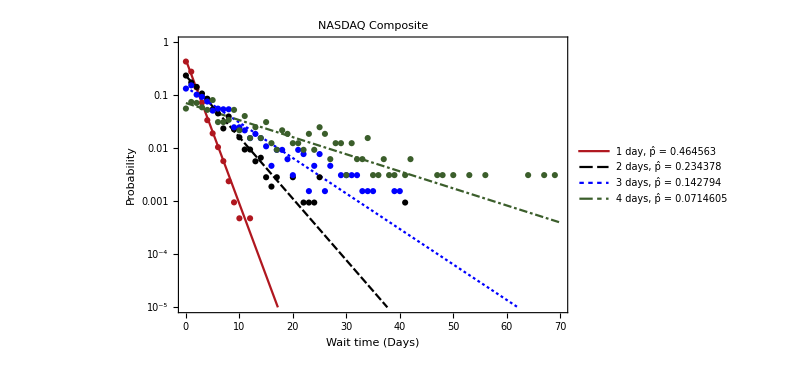
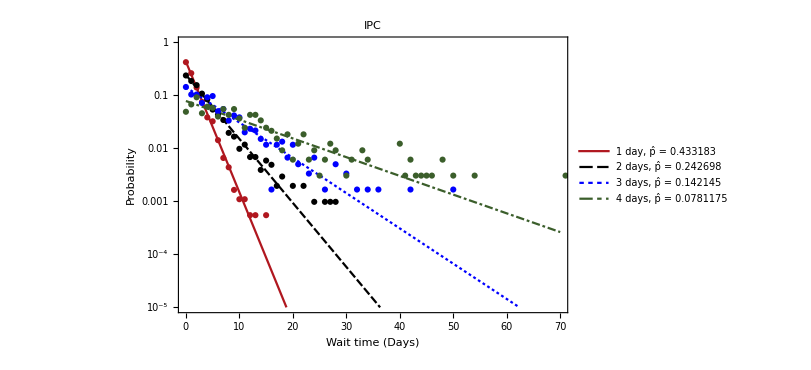
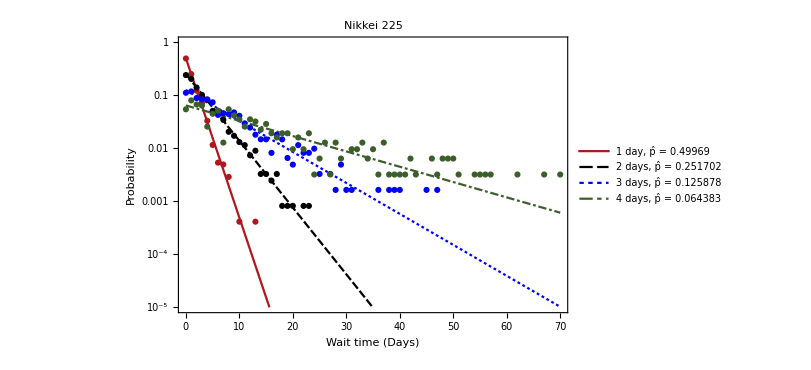

```mathematica
Map[DiscreteHistogramWaitTime,database]
```

Find fit automatically

```mathematica
FindWaitTimeDistributions[market_]:=Map[FindDistribution[WaitTime[market,#]]&,Range[4]];
FormatFindWaitTimeDist[market_]:=Labeled[Grid[Thread[{Range[4],FindWaitTimeDistributions[market]}]],market["Name"],Top];
Map[FormatFindWaitTimeDist,database]
```

{1 | GeometricDistribution[0.513066]
2 | GeometricDistribution[0.248634]
3 | GeometricDistribution[0.122337]
4 | GeometricDistribution[0.0650518]DJIA,1 | GeometricDistribution[0.464563]
2 | GeometricDistribution[0.234378]
3 | GeometricDistribution[0.142794]
4 | GeometricDistribution[0.0714605]NASDAQ Composite,1 | GeometricDistribution[0.433183]
2 | GeometricDistribution[0.242698]
3 | GeometricDistribution[0.142145]
4 | GeometricDistribution[0.0781175]IPC,1 | GeometricDistribution[0.49969]
2 | GeometricDistribution[0.251702]
3 | GeometricDistribution[0.125878]
4 | GeometricDistribution[0.064383]Nikkei 225}

Test for a geometric distribution

```mathematica
WaitTimeGOF[market_]:=Block[{dist,testData},
dist = Map[WaitTime[market,#]&,Range[4]];
testData = MapThread[{GeometricDistribution[#2],PearsonChiSquareTest[#1,GeometricDistribution[#2]]}&,{dist,{0.5,0.25,0.125,0.0625}}];

Labeled[
Grid[
Prepend[testData,{"Hypothesis","p-value"}],
Dividers->{{False,True},{False,True}}
],
market["Name"],
Top
]
];
```

```mathematica
Map[WaitTimeGOF,database]
```

{Hypothesis | p-value
GeometricDistribution[0.5] | 0.517962
GeometricDistribution[0.25] | 0.507141
GeometricDistribution[0.125] | 0.429097
GeometricDistribution[0.0625] | 0.192288DJIA,Hypothesis | p-value
GeometricDistribution[0.5] | 7.19167×10^-7
GeometricDistribution[0.25] | 0.0854396
GeometricDistribution[0.125] | 0.0101065
GeometricDistribution[0.0625] | 0.122488NASDAQ Composite,Hypothesis | p-value
GeometricDistribution[0.5] | 6.41239×10^-18
GeometricDistribution[0.25] | 0.524296
GeometricDistribution[0.125] | 0.00792484
GeometricDistribution[0.0625] | 0.00493737IPC,Hypothesis | p-value
GeometricDistribution[0.5] | 0.364495
GeometricDistribution[0.25] | 0.843388
GeometricDistribution[0.125] | 0.575041
GeometricDistribution[0.0625] | 0.403271Nikkei 225}

In time

```mathematica
RunDistributionInTime[market_,window_,skip_]:=DynamicModule[{part,hs},
part = Partition[market["Prices"],window,skip];
hs = Map[
SmoothHistogram[
WaitTimeForRuns[#,3],1,
PlotRange->{{0,50},{0,0.30}},
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait",bigFontSize],Style["PDF",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[3],{Right,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
PlotLabel->market["Name"]
]&,
part
];

Manipulate[hs[[i]],{i,1,Length[hs],1}]
];

GeneratePointsAndFit[prices_]:=Block[{waitTimes,histogramPts,ps,legend,fitted},
waitTimes = WaitTimeForRuns[prices];
histogramPts = Map[HistogramPoints,waitTimes];
ps = Map[EstimateP,waitTimes];
legend = MapThread[StringJoin[#1,", p̂ = ",ToString[#2]]&,{DayLegends[4],ps}];
fitted = Map[GenerateFitted[#,70]&,ps];

{Join[fitted,histogramPts],legend}
];
DiscreteHistogramWaitTimeEvolution[market_,window_,skip_]:=DynamicModule[{part,legend,data,hs},
part = Partition[market["Prices"],window,skip];

hs = Map[
({data,legend} = GeneratePointsAndFit[#];
ListLogPlot[
data,
Joined->{True,True,True,True,False,False,False,False},
PlotRange->{{0,70},{10^-15,1}},
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait time (Days)",15], Style["Probability",15]},
BaseStyle->FontSize->14,
PlotLabel->market["Name"],
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
ImageSize->600,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->Placed[LineLegend[legend,LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}]
])&,
part
];

Manipulate[hs[[i]],{i,1,Length[hs],1}]
];
```

```mathematica
Map[DiscreteHistogramWaitTimeEvolution[#,2000,200]&,database]
```

{,,,}

Estimate in time

```mathematica
EstimatePRunsEvolution[market_,duration_,window_,skip_]:=Block[{part,datesPart,hs,p},
part = Partition[market["Prices"],window,skip];
datesPart = Partition[market["Dates"],window,skip];
hs = Map[WaitTime[#,duration]&,part];

MapThread[{Last[#1],p/.FindDistributionParameters[#2,GeometricDistribution[p]]}&,{datesPart,hs}]
];
PlotPRunsEvolution[market_,window_,skip_]:=Block[{ps},
ps = Map[EstimatePRunsEvolution[market,#,window,skip]&,Range[3]];
DateListPlot[ps,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5,0.25,0.125}},
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotLabel->market["Name"],
PlotLegends->If[market["Name"]=="DJIA",Placed[LineLegend[DayLegends[3],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}],None]
]
];
```

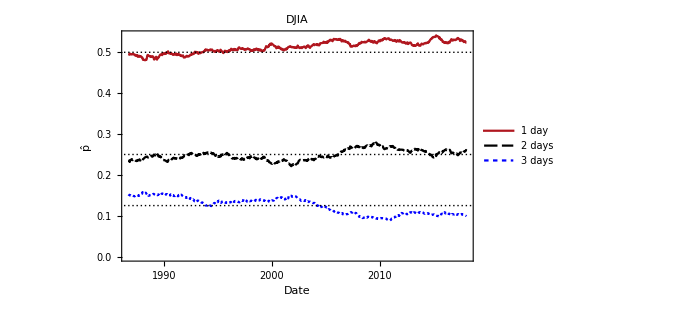
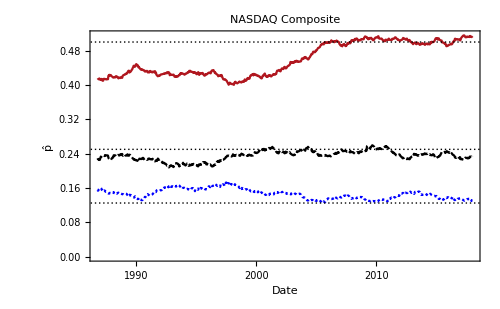
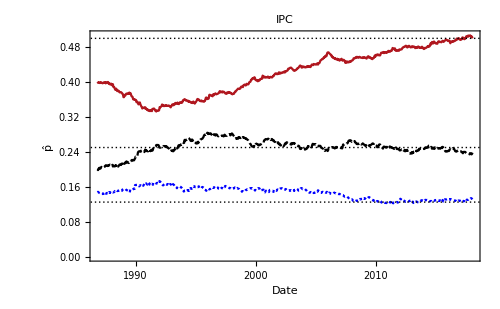
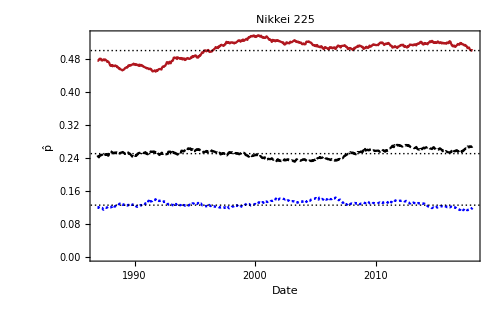

```mathematica
Map[PlotPRunsEvolution[#,2000,10]&,database]
```

Test in time

```mathematica
HypothesisGOF[wt_]:=MapThread[PearsonChiSquareTest[#1,GeometricDistribution[#2]]&,{wt,{0.5,0.25,0.125}}];
RunDistributionHypothesisGOFInTime[market_,window_,skip_]:=Block[{part,hs,pvalues},
part = Partition[market["Prices"],window,skip];
hs = Map[WaitTimeForRuns[#,3]&,part];
pvalues = Transpose[Map[HypothesisGOF,hs]];

DateListLogPlot[
pvalues,
{market["Dates"][[2000]],market["Dates"][[-1]]},
PlotLegends->If[market["Name"]=="DJIA",Placed[LineLegend[DayLegends[3],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],None],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p-Value",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0,1}},
Frame->True,
PlotLabel->market["Name"],
GridLines->{{},{0.01,0.05,0.1}}
]
];
```

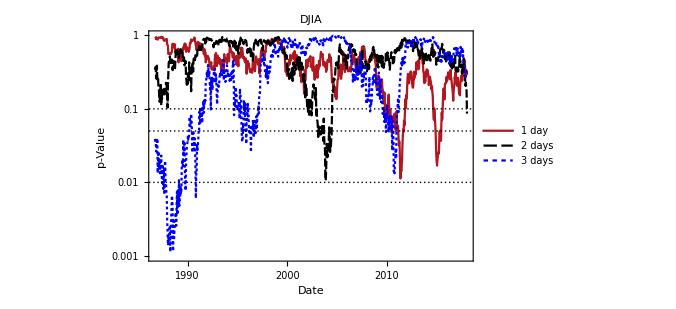
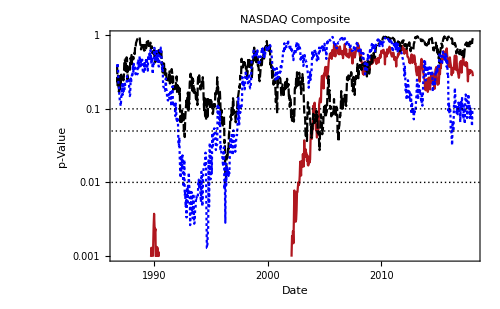
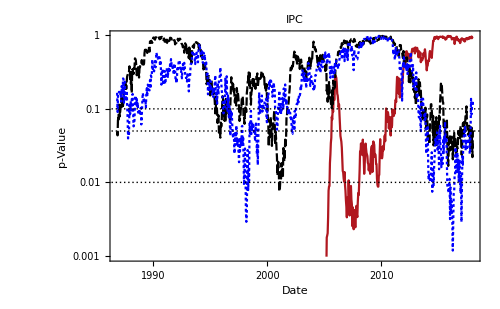
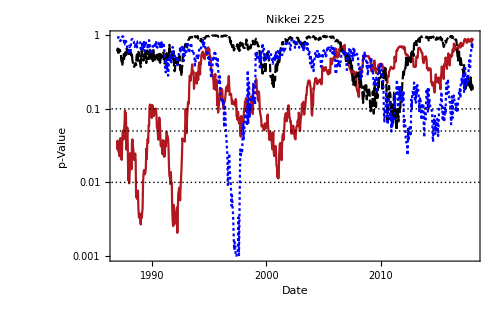

```mathematica
Map[RunDistributionHypothesisGOFInTime[#,2000,10]&,database]
```

TODO: 
- Comparar con caminata aleatoria
- Buscar bibliografia

Random walk comparison

### Trend duration

p-value estimation of geometric distribution

```mathematica
GenerateADPlotForRW[]:=Block[{priceWalk,trendDuration,adValues,indexedADValues,uppList,legend,plotData},
priceWalk = First[Normal[RandomFunction[WienerProcess[],{0,10000,1}]]][[All,2]];
trendDuration = TrendDuration[priceWalk];
adValues = ADPiValues[trendDuration,252,1];
indexedADValues = Transpose[{Range[Length[adValues]],adValues}];
uppList = Map[{{1, #},{Length[adValues],#}}&,{0.01,0.05,0.1}];
legend = Placed[LineLegend[{None,"α = 0.1","α = 0.05","α = 0.01"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}];

plotData = Join[{indexedADValues},uppList];
ListLogPlot[
plotData,
PlotRange->{Automatic,{Automatic,1}},
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["π-Value",15]},
BaseStyle->FontSize->13,
ImageSize->500,
Joined->{True,True,True,True,False},
PlotStyle->colors,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLegends->legend,
FrameTicks->True,
Frame->True
]
];
```

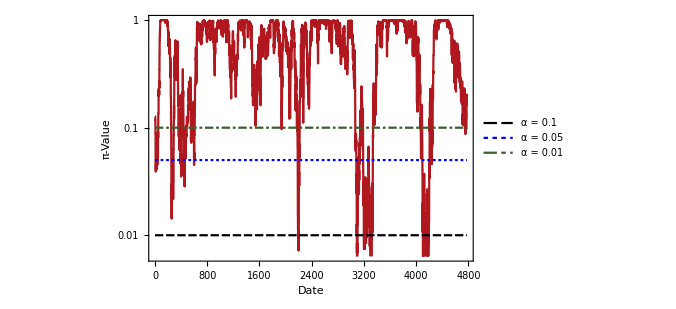
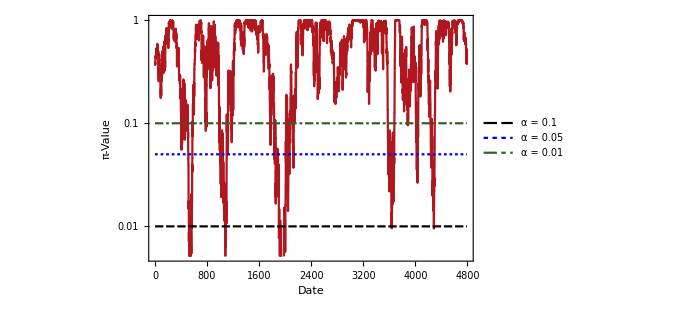
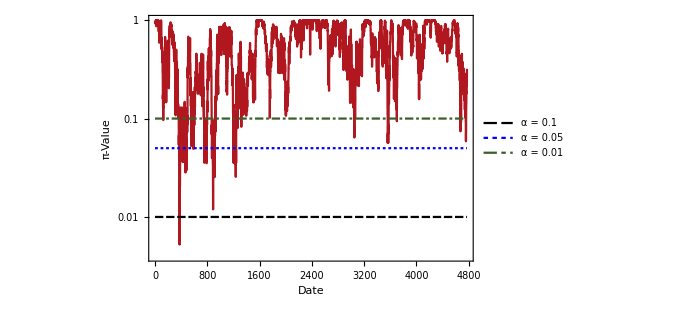
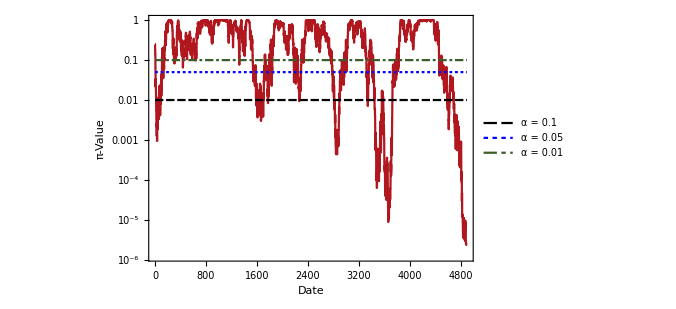
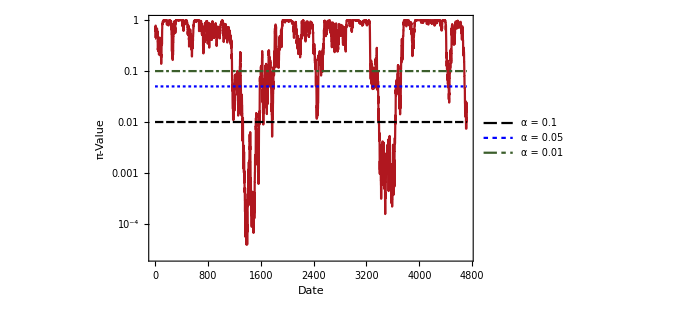

```mathematica
Table[GenerateADPlotForRW[],5]
```

```mathematica
πValueDistribution[window_,trials_]:=Block[{data,priceWalk,trendDuration,adValues},
data = Table[
priceWalk = First[Normal[RandomFunction[WienerProcess[],{0,10000,1}]]][[All,2]];
trendDuration = TrendDuration[priceWalk];
adValues = ADPiValues[trendDuration,window,1],
trials
];
Return[Flatten[data]]
];
πValueBadRatio[window_]:=Block[{pv},
pv = πValueDistribution[window,20];
N[Count[pv,x_/;x<0.05]/Length[pv]]
];
```

```mathematica
Map[πValueBadRatio,{100,300,500,700}]
```

{0.102019,0.159222,0.154216,0.161106}

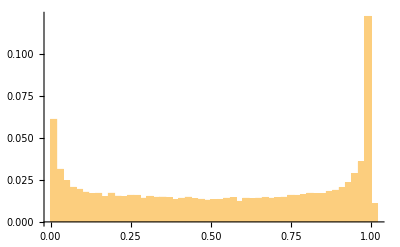

```mathematica
Histogram[πValueDistribution[252,20],50,"Probability"]
```

```mathematica
MatchLists[ls_]:=Block[{min},
min = Min[Map[Length,ls]];
Map[Take[#,min]&,ls]
];
CompareMarketToRandomWalk[market_]:=Block[{priceWalk,rdTD,marketTD,rdTDFormatted,marketTDFormatted},
priceWalk = First[Normal[RandomFunction[WienerProcess[],{0,10000,1}]]][[All,2]];
rdTD = TrendDuration[priceWalk];
marketTD = TrendDuration[market["Prices"]];
{rdTDFormatted,marketTDFormatted} = MatchLists[{rdTD,marketTD}];

Labeled[AndersonDarlingTest[rdTDFormatted,marketTDFormatted],market["Name"],Top]
];
```

```mathematica
ProgressMap[CompareMarketToRandomWalk,database]
```

{0.0738874DJIA,0.NASDAQ Composite,0.IPC,0.0103584Nikkei 225}

```mathematica
DispersionPlotRWVsMarket[market_]:=Block[{priceWalk,rdTD,marketTD,rdTDFormatted,marketTDFormatted},
priceWalk = First[Normal[RandomFunction[WienerProcess[],{0,10000,1}]]][[All,2]];
rdTD = TrendDuration[priceWalk];
marketTD = TrendDuration[market["Prices"]];
{rdTDFormatted,marketTDFormatted} = MatchLists[{rdTD,marketTD}];

ListPlot[
Transpose[{rdTDFormatted,marketTDFormatted}],
PlotRange->All,
PlotStyle->PointSize[Medium],
PlotTheme->"Monochrome",
Frame->True,
PlotLabel->market["Name"]
]
];
```

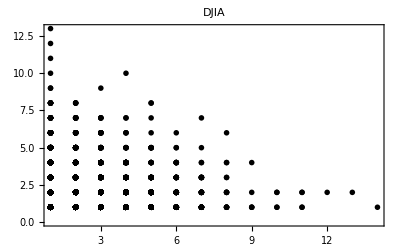
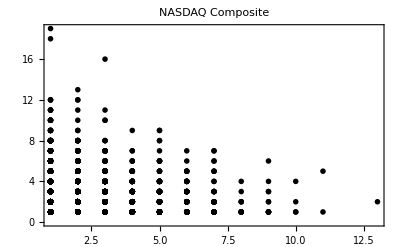
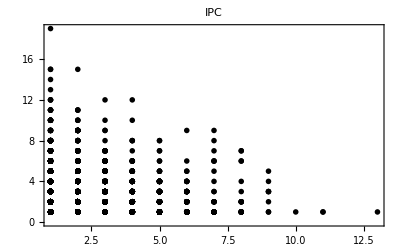
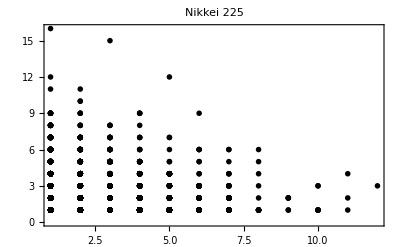

```mathematica
ProgressMap[DispersionPlotRWVsMarket,database]
```

```mathematica
EstimatePInTimeRW[window_,skip_]:=Block[{priceWalk,p,ps,trendDuration,part,datesPart,pricesPart,outDates},
priceWalk = First[Normal[RandomFunction[WienerProcess[],{0,10000,1}]]][[All,2]];
trendDuration = TrendDuration[priceWalk];
part = Partition[trendDuration,window,skip];

ps = Map[p/.FindDistributionParameters[#-1,GeometricDistribution[p]]&,part];

Return[ps];
]
```

```mathematica
estimatedP = Table[EstimatePInTimeRW[252,10],5];
```

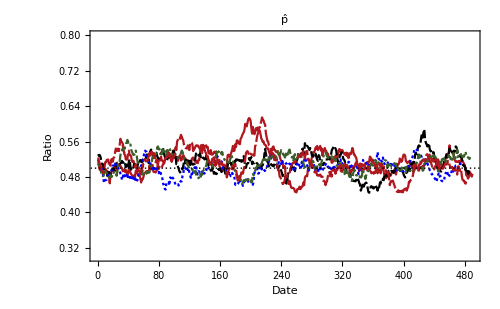

```mathematica
ListPlot[
estimatedP,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotLabel->"p̂",
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.3,0.8}},
Frame->True
]
```

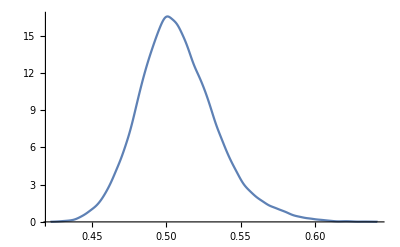

```mathematica
estimatedP = Table[EstimatePInTimeRW[252,10],100];
SmoothHistogram[Flatten[estimatedP]]
```

```mathematica
marketsP = database[[All,"EstimatedPInTime"]][[All,All,2]];
```

```mathematica
plotData = Join[{Flatten[estimatedP]},marketsP];
```

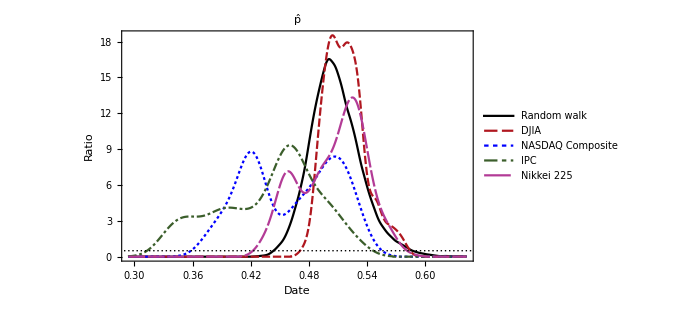

```mathematica
SmoothHistogram[
plotData,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5}},
PlotLabel->"p̂",
PlotStyle->{GrayLevel[0],RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.7000000000000001, 0.23, 0.59],RGBColor[0.92, 0.52, 0.],RGBColor[0., 0.55, 0.66]},
Frame->True,
PlotLegends->Placed[LineLegend[Prepend[database[[All,"Name"]],"Random walk"],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}]
]
```

### Waiting time

```mathematica
EstimatePRunsEvolutionRW[duration_,window_,skip_]:=Block[{priceWalk,part,datesPart,hs,p},
priceWalk = First[Normal[RandomFunction[WienerProcess[],{0,10000,1}]]][[All,2]];
part = Partition[priceWalk,window,skip];
datesPart = Partition[Range[Length[priceWalk]],window,skip];
hs = Map[WaitTime[#,duration]&,part];

MapThread[{Last[#1],p/.FindDistributionParameters[#2,GeometricDistribution[p]]}&,{datesPart,hs}]
];
PlotPRunsEvolutionRW[window_,skip_]:=Block[{ps},
ps = Map[EstimatePRunsEvolutionRW[#,window,skip]&,Range[3]];
ListPlot[ps,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p̂",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{{},{0.5,0.25,0.125}},
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotLegends->Placed[LineLegend[DayLegends[3],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Bottom}],
Frame->True
]
];
```

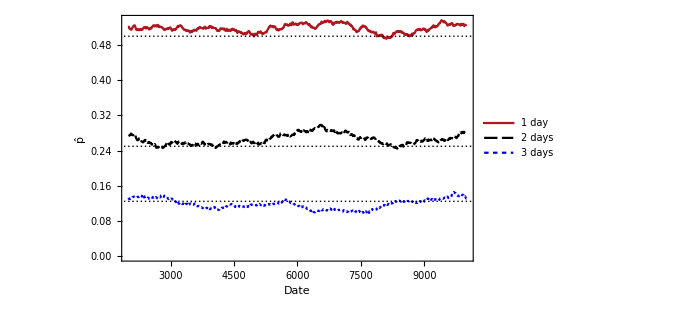
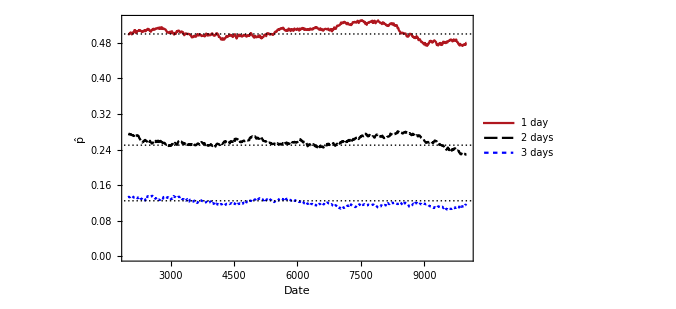
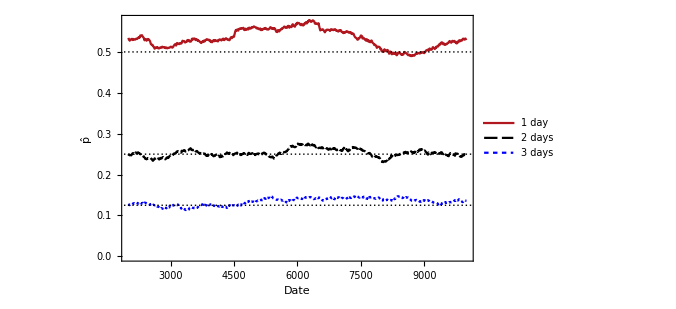
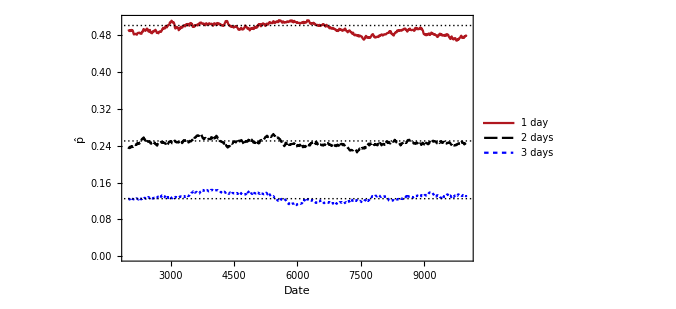
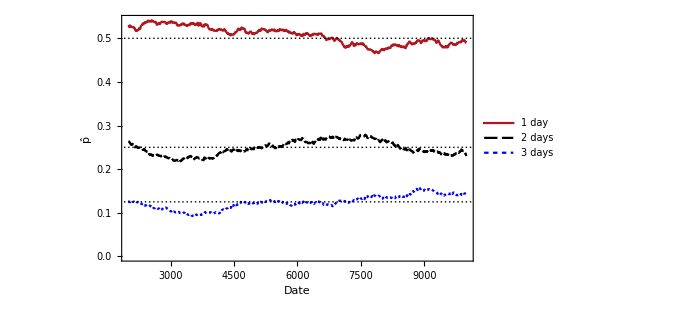

```mathematica
Table[PlotPRunsEvolutionRW[2000,10],5]
```

```mathematica
RunDistributionHypothesisGOFInTimeRW[window_,skip_]:=Block[{priceWalk,part,hs,pvalues},
priceWalk = First[Normal[RandomFunction[WienerProcess[],{0,10000,1}]]][[All,2]];
part = Partition[priceWalk,window,skip];
hs = Map[WaitTimeForRuns[#,3]&,part];
pvalues = Transpose[Map[HypothesisGOF,hs]];

ListLogPlot[
pvalues,
PlotLegends->Placed[LineLegend[DayLegends[3],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["p-Value",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
PlotStyle->colors,
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0,1}},
Frame->True,
GridLines->{{},{0.01,0.05,0.1}}
]
];
```

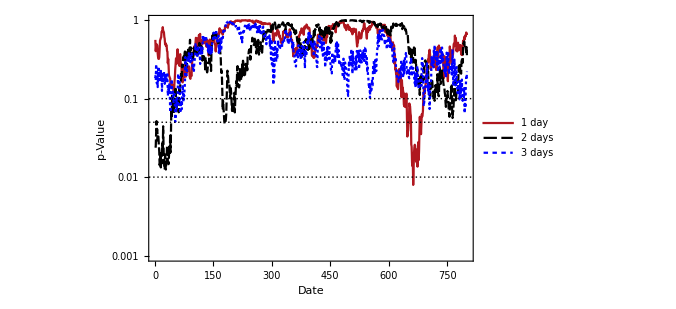
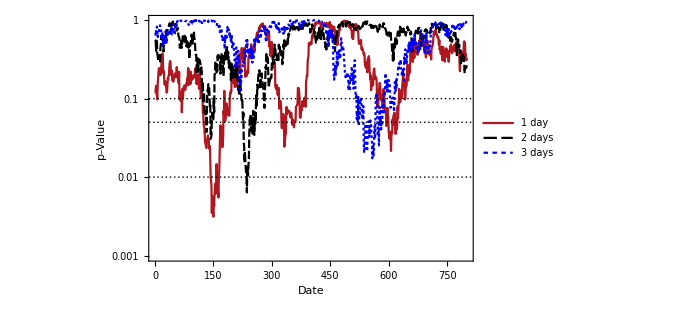
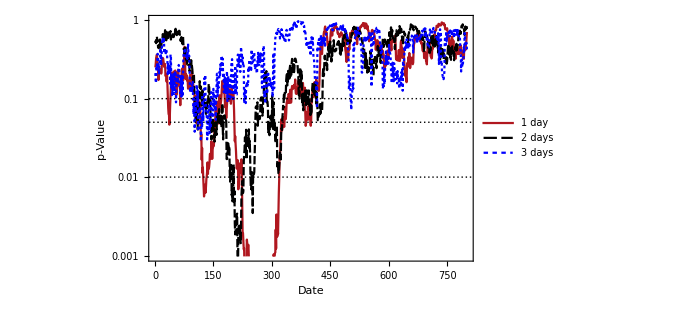
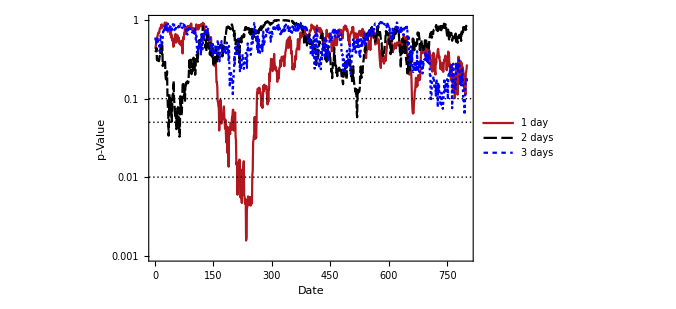
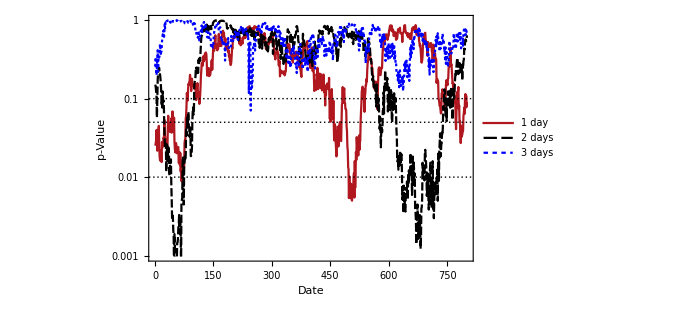

```mathematica
Table[RunDistributionHypothesisGOFInTimeRW[2000,10],5]
```